```mathematica
raw = Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/results.json"];
raw = Association[#]&/@raw
```

{<|quad→Q5FF,axis→X,magnetConfigKey→upstream,PENT_xCenter→-0.0000189564,PENT_yCenter→6.07894×10^-19|>,<|quad→Q5FF,axis→X,magnetConfigKey→PENT,PENT_xCenter→-0.000025814,PENT_yCenter→3.31467×10^-19|>,<|quad→Q5FF,axis→X,magnetConfigKey→downstream,PENT_xCenter→-0.0000325637,PENT_yCenter→4.45417×10^-19|>,<|quad→Q5FF,axis→Y,magnetConfigKey→upstream,PENT_xCenter→1.69909×10^-18,PENT_yCenter→-0.0000482025|>,<|quad→Q5FF,axis→Y,magnetConfigKey→PENT,PENT_xCenter→-1.9254×10^-17,PENT_yCenter→-0.0000302165|>,<|quad→Q5FF,axis→Y,magnetConfigKey→downstream,PENT_xCenter→-8.5489×10^-18,PENT_yCenter→-0.0000143317|>,<|quad→Q4FF,axis→X,magnetConfigKey→upstream,PENT_xCenter→-0.000041803,PENT_yCenter→1.58303×10^-18|>,<|quad→Q4FF,axis→X,magnetConfigKey→PENT,PENT_xCenter→-0.0000481323,PENT_yCenter→-1.18292×10^-18|>,<|quad→Q4FF,axis→X,magnetConfigKey→downstream,PENT_xCenter→-0.0000538918,PENT_yCenter→1.51383×10^-18|>,<|quad→Q4FF,axis→Y,magnetConfigKey→upstream,PENT_xCenter→1.09899×10^-17,PENT_yCenter→-0.0000396504|>,<|quad→Q4FF,axis→Y,magnetConfigKey→PENT,PENT_xCenter→1.59774×10^-17,PENT_yCenter→-0.0000205837|>,<|quad→Q4FF,axis→Y,magnetConfigKey→downstream,PENT_xCenter→-2.30401×10^-17,PENT_yCenter→-4.9093×10^-6|>,<|quad→Q3FF,axis→X,magnetConfigKey→upstream,PENT_xCenter→0.00006855,PENT_yCenter→-6.68625×10^-20|>,<|quad→Q3FF,axis→X,magnetConfigKey→PENT,PENT_xCenter→0.0000768147,PENT_yCenter→-1.19446×10^-18|>,<|quad→Q3FF,axis→X,magnetConfigKey→downstream,PENT_xCenter→0.000083275,PENT_yCenter→-1.20284×10^-18|>,<|quad→Q3FF,axis→Y,magnetConfigKey→upstream,PENT_xCenter→2.23562×10^-17,PENT_yCenter→0.0000318657|>,<|quad→Q3FF,axis→Y,magnetConfigKey→PENT,PENT_xCenter→-1.01676×10^-17,PENT_yCenter→0.0000137778|>,<|quad→Q3FF,axis→Y,magnetConfigKey→downstream,PENT_xCenter→-1.82294×10^-17,PENT_yCenter→-8.541×10^-7|>,<|quad→Q2FF,axis→X,magnetConfigKey→upstream,PENT_xCenter→0.000116133,PENT_yCenter→-2.56131×10^-19|>,<|quad→Q2FF,axis→X,magnetConfigKey→PENT,PENT_xCenter→0.000111498,PENT_yCenter→-1.19061×10^-18|>,<|quad→Q2FF,axis→X,magnetConfigKey→downstream,PENT_xCenter→0.000108673,PENT_yCenter→-1.01363×10^-18|>,<|quad→Q2FF,axis→Y,magnetConfigKey→upstream,PENT_xCenter→-1.8292×10^-17,PENT_yCenter→-0.0000645019|>,<|quad→Q2FF,axis→Y,magnetConfigKey→PENT,PENT_xCenter→-2.68074×10^-18,PENT_yCenter→-0.000064888|>,<|quad→Q2FF,axis→Y,magnetConfigKey→downstream,PENT_xCenter→-2.31744×10^-17,PENT_yCenter→-0.0000649235|>,<|quad→Q1FF,axis→X,magnetConfigKey→upstream,PENT_xCenter→-0.000111216,PENT_yCenter→-7.66207×10^-19|>,<|quad→Q1FF,axis→X,magnetConfigKey→PENT,PENT_xCenter→-0.000108656,PENT_yCenter→-8.04182×10^-20|>,<|quad→Q1FF,axis→X,magnetConfigKey→downstream,PENT_xCenter→-0.000106858,PENT_yCenter→2.47834×10^-19|>,<|quad→Q1FF,axis→Y,magnetConfigKey→upstream,PENT_xCenter→-2.11497×10^-17,PENT_yCenter→0.000215398|>,<|quad→Q1FF,axis→Y,magnetConfigKey→PENT,PENT_xCenter→-5.21899×10^-18,PENT_yCenter→0.000205706|>,<|quad→Q1FF,axis→Y,magnetConfigKey→downstream,PENT_xCenter→2.54062×10^-17,PENT_yCenter→0.000197117|>,<|quad→Q0FF,axis→X,magnetConfigKey→upstream,PENT_xCenter→0.0000551753,PENT_yCenter→-1.35852×10^-18|>,<|quad→Q0FF,axis→X,magnetConfigKey→PENT,PENT_xCenter→0.0000534465,PENT_yCenter→-1.03209×10^-18|>,<|quad→Q0FF,axis→X,magnetConfigKey→downstream,PENT_xCenter→0.0000515657,PENT_yCenter→1.07719×10^-18|>,<|quad→Q0FF,axis→Y,magnetConfigKey→upstream,PENT_xCenter→6.12743×10^-17,PENT_yCenter→-0.0000602262|>,<|quad→Q0FF,axis→Y,magnetConfigKey→PENT,PENT_xCenter→3.26845×10^-18,PENT_yCenter→-0.000058172|>,<|quad→Q0FF,axis→Y,magnetConfigKey→downstream,PENT_xCenter→-8.81699×10^-18,PENT_yCenter→-0.0000559506|>}

```mathematica
activeData = Select[raw,#quad == "Q5FF" && #axis =="X"&];
```

```mathematica
plotFunc[data_,label_]:=(
ListPlot[{#}&/@data,PlotRange->{{-200,200},{-200,200}},AspectRatio->1,ImageSize->800,LabelStyle->20,PlotLabel->label]
)
```

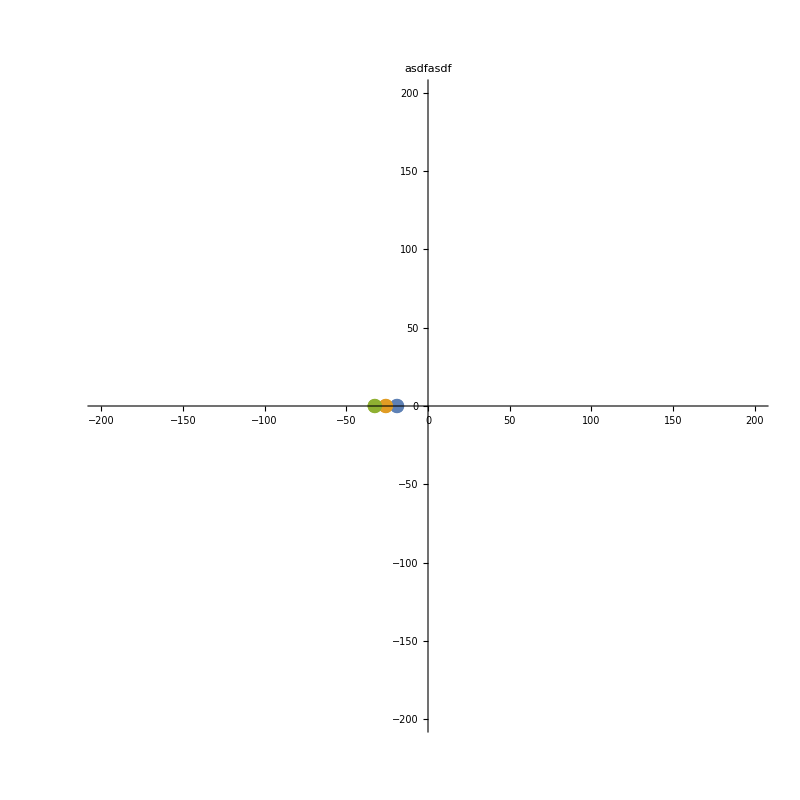

```mathematica
plotFunc[
10^6{#["PENT_xCenter"],#["PENT_yCenter"]}&/@activeData,
"asdfasdf"
]
```

```mathematica
DeleteDuplicates[raw[[All,"quad"]]]
```

{Q5FF,Q4FF,Q3FF,Q2FF,Q1FF,Q0FF}

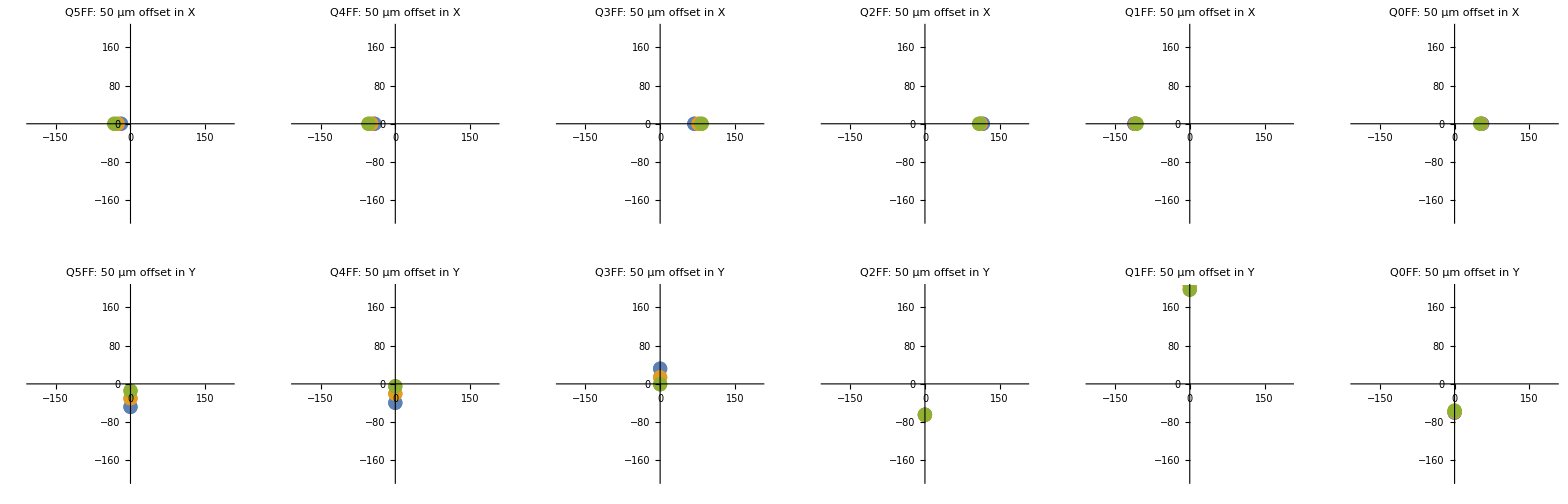

```mathematica
imgArr = Table[
activeData = Select[raw,#quad == quad && #axis ==axis&];

plotFunc[
10^6{#["PENT_xCenter"],#["PENT_yCenter"]}&/@activeData,
quad<>": 50 μm offset in "<>axis
],
{axis,{"X","Y"}},
{quad,DeleteDuplicates[raw[[All,"quad"]]]}


];
GraphicsGrid[imgArr,
ImageSize->3200]
```

```mathematica
tmpData = Table[
activeData = Select[raw,#quad == quad && #axis ==axis&];

{
quad,
axis,
10^6(activeData[[1,"PENT_xCenter"]] - activeData[[3,"PENT_xCenter"]]),
10^6(activeData[[1,"PENT_yCenter"]] - activeData[[3,"PENT_yCenter"]])
},

{quad,DeleteDuplicates[raw[[All,"quad"]]]},
{axis,{"X","Y"}}



]
```

{{{Q5FF,X,13.6073,1.62477×10^-13},{Q5FF,Y,1.0248×10^-11,-33.8708}},{{Q4FF,X,12.0888,6.91987×10^-14},{Q4FF,Y,3.403×10^-11,-34.7411}},{{Q3FF,X,-14.725,1.13598×10^-12},{Q3FF,Y,4.05856×10^-11,32.7198}},{{Q2FF,X,7.4597,7.57499×10^-13},{Q2FF,Y,4.88237×10^-12,0.4216}},{{Q1FF,X,-4.3586,-1.01404×10^-12},{Q1FF,Y,-4.65559×10^-11,18.2816}},{{Q0FF,X,3.6096,-2.43571×10^-12},{Q0FF,Y,7.00913×10^-11,-4.2756}}}

{13.6073,12.0888,-14.725,7.4597,-4.3586,3.6096}

{-33.8708,-34.7411,32.7198,0.4216,18.2816,-4.2756}

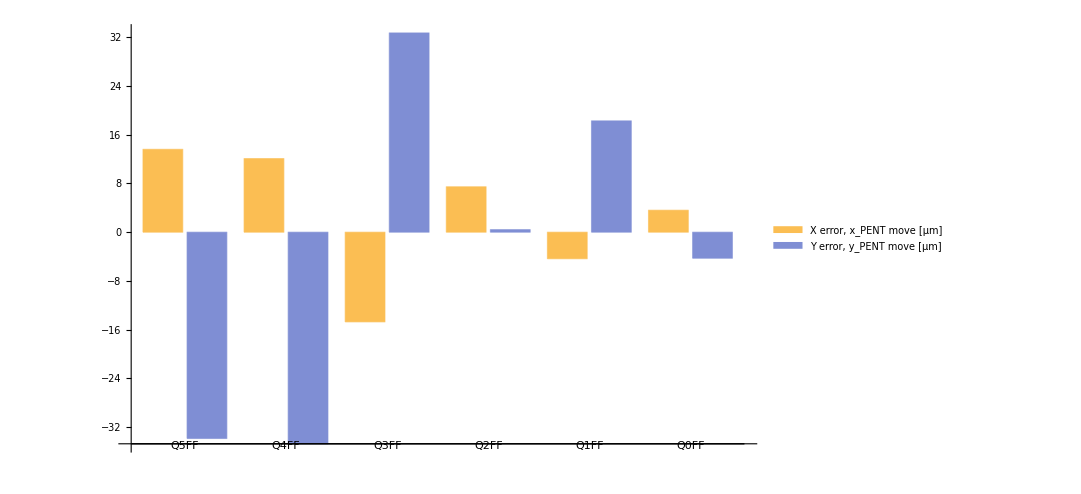

```mathematica
BarChart[Transpose[{
tmpData[[All,All,3]][[All,1]],
tmpData[[All,All,4]][[All,2]]
}],
ImageSize->800,
ChartLegends->Placed[{"X error, x_PENT move [μm]","Y error, y_PENT move [μm]"},{0.2,0.9}],
LabelStyle->20,
ChartLabels->{{"Q5FF","Q4FF","Q3FF","Q2FF","Q1FF","Q0FF"},None}
]
```

```mathematica
Table[
activeData = Select[raw,#quad == quad && #axis ==axis&];



Print["50 μm ", quad," error in ",axis, " moves x_PENT by ", Round[10^6(activeData[[1,"PENT_xCenter"]] - activeData[[3,"PENT_xCenter"]]),0.1], " μm and y_PENT by ",Round[10^6(activeData[[1,"PENT_yCenter"]] - activeData[[3,"PENT_yCenter"]]),0.1], " μm"],
{quad,DeleteDuplicates[raw[[All,"quad"]]]},
{axis,{"X","Y"}}



];
```

50 μm Q5FF error in X moves x_PENT by 13.6 μm and y_PENT by 0. μm

50 μm Q5FF error in Y moves x_PENT by 0. μm and y_PENT by -33.9 μm

50 μm Q4FF error in X moves x_PENT by 12.1 μm and y_PENT by 0. μm

50 μm Q4FF error in Y moves x_PENT by 0. μm and y_PENT by -34.7 μm

50 μm Q3FF error in X moves x_PENT by -14.7 μm and y_PENT by 0. μm

50 μm Q3FF error in Y moves x_PENT by 0. μm and y_PENT by 32.7 μm

50 μm Q2FF error in X moves x_PENT by 7.5 μm and y_PENT by 0. μm

50 μm Q2FF error in Y moves x_PENT by 0. μm and y_PENT by 0.4 μm

50 μm Q1FF error in X moves x_PENT by -4.4 μm and y_PENT by 0. μm

50 μm Q1FF error in Y moves x_PENT by 0. μm and y_PENT by 18.3 μm

50 μm Q0FF error in X moves x_PENT by 3.6 μm and y_PENT by 0. μm

50 μm Q0FF error in Y moves x_PENT by 0. μm and y_PENT by -4.3 μm

6.12743×10^-17